# 主成分分析（PCA）

## 0. 系统内置函数：PrincipalComponents

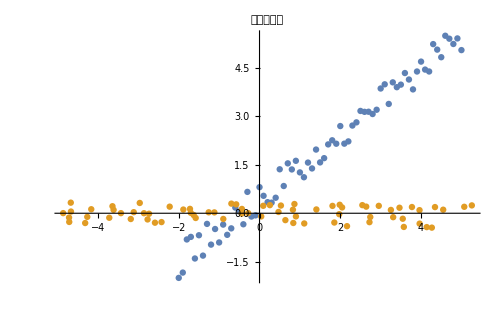
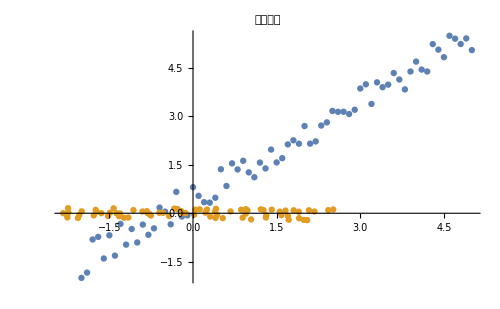

```mathematica
SeedRandom[5];
data=Table[{x,x+RandomReal[]},{x,-2,5,0.1}];(*数据*)


pVData=PrincipalComponents[data,Method->"Covariance"];(*协方差矩阵*)
pRData=PrincipalComponents[data,Method->"Correlation"];(*相关矩阵*)

Row[{
ListPlot[{data,pVData},ImageSize->500,PlotLabel->Style["协方差矩阵",Bold,20,FontFamily->"微软雅黑"]],
ListPlot[{data,pRData},ImageSize->500,PlotLabel->Style["相关矩阵",Bold,20,FontFamily->"微软雅黑"]]
}]
```

## 1. 解释

### 1.1 协方差矩阵

```mathematica
nData=data-ConstantArray[Mean[data],Length[data]];(*消除均值*)
vM=Covariance[data];(*协方差矩阵*)
a=Transpose[Eigenvectors[vM]];(*协方差矩阵的特征向量：转为列向量*)
pVData2=nData.a;(*主成分，每列与内置函数生成的主成分差一个符号*)
pV=Eigenvalues[vM];(*主成分每列的方差*)
```

```mathematica
pVData+pVData2//Chop
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

### 1.2 相关性矩阵？

```mathematica
(data-ConstantArray[Mean[data],Length[data]]).Transpose[Eigenvectors[Correlation[data]]]
(data-ConstantArray[Mean[data],Length[data]]).Transpose[Eigenvectors[Covariance[data]]]
```